```mathematica
funTrimList[parList_]:=Module[{listBase,listTrim,inc,l,place},
listBase=Take[parList,3];
listTrim=Partition[Drop[parList,3],2];
l=Length[listTrim];
For[inc=1,inc≤ l,inc++,

If[MemberQ[N[listTrim[[inc]]],0.],
place=False;,
AppendTo[listBase,listTrim[[inc]]];
];

];

Return[Flatten[listBase]];
];


compConstrFun[k_]:=Module[{eqBase,h0eq,i,parBase,eliBase,g0eq,kgeq},
eqBase={h0== h+hd,d0== d+hd,kd== hd/(h*d)};
h0eq={h0,h+hd};
parBase={h0,d0,kd};
eliBase={h,d};
For[i=0,i≤ k,i++,
If[i>0,
g0eq={ToExpression["g0"<>ToString[i]]== ToExpression["g"<>ToString[i]]+ToExpression["hg"<>ToString[i]]};
kgeq={ToExpression["kg"<>ToString[i]]== ToExpression["hg"<>ToString[i]]/(ToExpression["g"<>ToString[i]]*ToExpression["h"])};
AppendTo[eqBase,g0eq[[1]]];
AppendTo[parBase,Symbol["g0"<>ToString@i]];
AppendTo[eliBase,Symbol["g"<>ToString@i]];
AppendTo[eqBase,kgeq[[1]]];
AppendTo[parBase,Symbol["kg"<>ToString@i]];
AppendTo[eliBase,Symbol["hg"<>ToString@i]];
h0eq={h0eq[[1]],h0eq[[2]]+ToExpression["hg"<>ToString[i]]};
eqBase=ReplacePart[eqBase,1-> h0eq[[1]]== h0eq[[2]]];

];

];

Return[{eqBase,parBase,eliBase}]
];

compElimFunHD[parm_]:=compElimFunHD[parm]=Module[{result,sol,brac,l,eliHD},
l=Length[parm];
result=compConstrFun[(l-3)/2];
eliHD=Eliminate[result[[1]]/.Thread[result[[2]]-> parm],result[[3]]];
sol=hd/.NSolve[eliHD,hd];
Return[sol];

];

compResultFunHD[input_]:=compResultFunHD[input]=Module[{result,sol,brac,l,par,posZero,trimPar},
par=N[input];
Off[Select::normal];
l=Length[par];
If[(AllTrue[par,NumericQ]&&OddQ[l]),
If[(par[[1]]==0.||par[[2]]==0.),
sol=0.;,
	If[MemberQ[Drop[par,3],0.],
	trimPar=funTrimList[par];
	sol=compElimFunHD[trimPar];,
	sol=compElimFunHD[par];
	];
];

	result=Select[Re[sol],0.≤#≤par[[1]]&&0.≤#≤par[[2]]&];
	brac=First[result];
,brac="False"];

Return[brac];
];
```

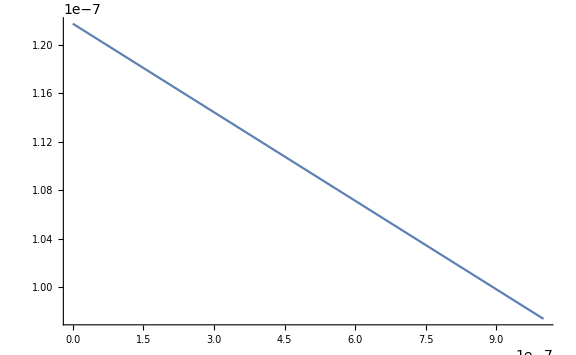

Save-Sim

h0==h+hd+hg1+hg10+hg2+hg3+hg4+hg5+hg6+hg7+hg8+hg9
d0==d+hd
kd==hd/(d h)
g01==g1+hg1
kg1==hg1/(g1 h)
g02==g2+hg2
kg2==hg2/(g2 h)
g03==g3+hg3
kg3==hg3/(g3 h)
g04==g4+hg4
kg4==hg4/(g4 h)
g05==g5+hg5
kg5==hg5/(g5 h)
g06==g6+hg6
kg6==hg6/(g6 h)
g07==g7+hg7
kg7==hg7/(g7 h)
g08==g8+hg8
kg8==hg8/(g8 h)
g09==g9+hg9
kg9==hg9/(g9 h)
g010==g10+hg10
kg10==hg10/(g10 h)

```mathematica
h0in=5*^-6;
d0in=5*^-6;
kequhdin=1*^8;

ga1=200*^-6; (*Steroids*)
ka1=1*^8;

ga2=1.0*^-5; (*Cholesterol*)
ka2=1*^4;

ga3=1.0*^-6; (*Fatty Acids*)
ka3=1*^3;

ga4=1.0*^-6; (*Putrescine/Spermidine*)
ka4=1*^6;

ga5=7.0*^-3; (*Ca2+*)
ka5=1*^3;

ga6=155*^-3; (*Na+*)
ka6=1*^2;

ga7=15*^-3; (*K+*)
ka7=1*^2;

ga8=6.7*^-3; (*Hexosamine*)
ka8=1*^3;

ga9=1*^-4; (*Aminoacids*)
ka9=1*^4;

ga10=1.0*^-6; (*Memantine*)
ka10=1*^13;


simData=Table[{N[i],compResultFunHD[{h0in,d0in,kequhdin,ga1,ka1,ga2,ka2,ga3,ka3,ga4,ka4,ga5,ka5,ga6,ka6,ga7,ka7,ga8,ka8,ga9,ka9,i,ka10}]},{i,0.,ga10,ga10/50.}];

inputs={{"Quantity","Value"},
{"Mode","Competition"},
{"conc(H)",h0in},
{"conc(D)",d0in},
{"Kequ(D)",kequhdin}
};
header={"conc","Signal"};
units={"M","INT"};
column1=Flatten[inputs[[All,1]]];
column2=Flatten[inputs[[All,2]]];
signaloutput=simData;

put=Prepend[Prepend[signaloutput,units],header];
output=Join[put,List/@column1,List/@column2,2];


Quiet[exportbutton3=Button["Save-Sim",Export[SystemDialogInput["FileSave",".csv"],output],Method->"Queued"]];



signaloutput=simData;

put=Prepend[Prepend[signaloutput,units],header];
output=Join[put,List/@column1,List/@column2,2];

Show[ListLinePlot[simData],ImageSize->Large]
Print[exportbutton3]
compConstrFun[(Length[{h0in,d0in,kequhdin,ga1,ka1,ga2,ka2,ga3,ka3,ga4,ka4,ga5,ka5,ga6,ka6,ga7,ka7,ga8,ka8,ga9,ka9,ga10,ka10}]-3)/2][[1]]//TableForm
```

```mathematica
Re[compElimFunHD[{h0in,d0in,kequhdin,ga1,ka1,ga2,ka2}]]
Select[Re[%],0.≤#≤h0in&&0.≤#≤d0in&]
```

{-1.85733×10^-9,1.84363×10^-9,1.00667×10^-6,0.000148013}

{1.84363×10^-9}

```mathematica
"False"
compResultFunHD[{h0in,d0in*1.1,kequhdin,ga1,ka1,ga2,ka2}]
```

False

{-2.00968×10^-9,1.99474×10^-9,1.1071×10^-6,0.000153013}

```mathematica
fitsignal=NonlinearModelFit[simData,compElimFunHD[{h0,2,kd}],{{kd,19.}},h0];
```

NonlinearModelFit::eqineq: Constraints in {(0.5 (1.+2. kd+h0 kd+√(-8. h0 kd^2+(-1.+Times[«2»]+Times[«3»])^2)))/kd} are not all equality or inequality constraints. With the exception of integer domain constraints for linear programming, domain constraints or constraints with Unequal (!=) are not supported.

```mathematica
compElimFunHD[{h0,1,kd,9,8}]
```

{-(0.333333 (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2))/(-8. kd+kd^2)-(0.419974 (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2)))/((-8. kd+kd^2) (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3))+1/(-8. kd+kd^2)0.264567 (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3),-(0.333333 (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2))/(-8. kd+kd^2)+((0.209987+0.363708 ⅈ) (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2)))/((-8. kd+kd^2) (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3))-1/(-8. kd+kd^2)(0.132283-0.229122 ⅈ) (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3),-(0.333333 (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2))/(-8. kd+kd^2)+((0.209987-0.363708 ⅈ) (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2)))/((-8. kd+kd^2) (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3))-1/(-8. kd+kd^2)(0.132283+0.229122 ⅈ) (-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6+√((-1024.+24960. kd-3072. h0 kd-244080. kd^2+54912. h0 kd^2-3072. h0^2 kd^2+883090. kd^3-288720. h0 kd^3+30336. h0^2 kd^3-1024. h0^3 kd^3+23067. kd^4+37374. h0 kd^4-7824. h0^2 kd^4+384. h0^3 kd^4-195. kd^5-315. h0 kd^5+558. h0^2 kd^5-48. h0^3 kd^5-2. kd^6+6. h0 kd^6-6. h0^2 kd^6+2. h0^3 kd^6)^2+4. (-1. (8.-65. kd+8. h0 kd-2. kd^2-1. h0 kd^2)^2+3. (-8. kd+kd^2) (73. kd-8. h0 kd+kd^2+2. h0 kd^2))^3))^(1/3)}